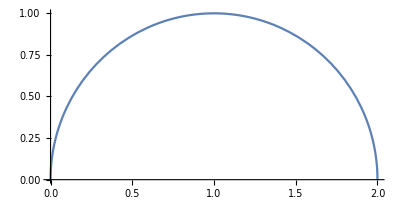

```mathematica
ParametricPlot[{1-Cos[x],Sin[x]},{x,0,Pi}]
```

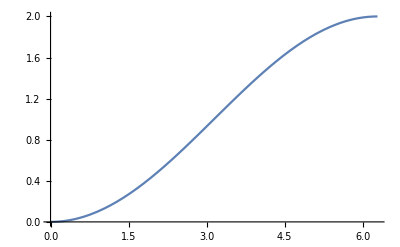

```mathematica
Plot[1 - Cos[x/2], {x, 0, 2*Pi}]
```

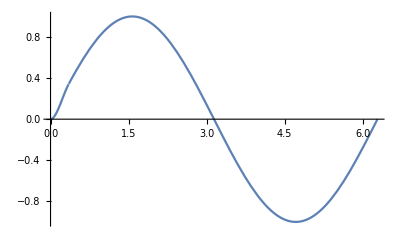

```mathematica
Plot[Piecewise[{{InterpolatingPolynomial[{{0,0,0},{Pi/9,Sin[Pi/9],Cos[Pi/9]}},x],x<Pi/9},{Sin[x],x>=Pi/9}}], 
{x, 0, 2*Pi}]
```

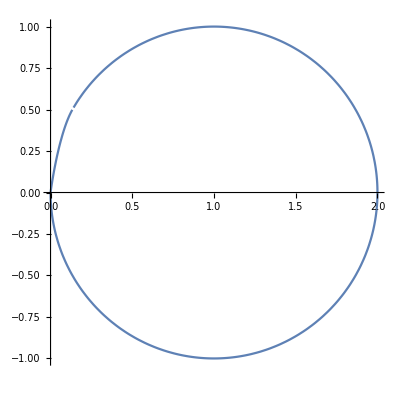

```mathematica
ParametricPlot[{1-Cos[x],Piecewise[{{InterpolatingPolynomial[{{0,0,0},{Pi/6,Sin[Pi/6],Cos[Pi/6]}},x],x<Pi/6},{Sin[x],x>=Pi/9}}]},{x,0,2*Pi}]
```

```mathematica
D[Piecewise[{{InterpolatingPolynomial[{{0,0,0},{Pi/9,Sin[Pi/9],Cos[Pi/9]}},x],x<=Pi/9},{Sin[x],x>Pi/9}}],x]
```

Piecewise[{{(9 x^2 (9 π Cos[π/9]-162 Sin[π/9]))/π^3+(18 x (-π^2 Cos[π/9]+9 π x Cos[π/9]+27 π Sin[π/9]-162 x Sin[π/9]))/π^3, x<π/9}, {Cos[π/9], x==π/9}, {Cos[x], True}}]

```mathematica
InterpolatingPolynomial[{{0,0,0},{Pi/9,Sin[Pi/9],Cos[Pi/9]}},x]
```

```mathematica
x^2 ((81 Sin[π/9])/π^2+(9 (-π/9+x) (-(81 Sin[π/9])/π^2+(9 (Cos[π/9]-(9 Sin[π/9])/π))/π))/π)
```

```mathematica
Expand[%]
```

```mathematica
-(9 x^2 Cos[π/9])/π+(81 x^3 Cos[π/9])/π^2+(243 x^2 Sin[π/9])/π^2-(1458 x^3 Sin[π/9])/π^3
D[%]
```

-(9 x^2 Cos[π/9])/π+(81 x^3 Cos[π/9])/π^2+(243 x^2 Sin[π/9])/π^2-(1458 x^3 Sin[π/9])/π^3

-(9 x^2 Cos[π/9])/π+(81 x^3 Cos[π/9])/π^2+(243 x^2 Sin[π/9])/π^2-(1458 x^3 Sin[π/9])/π^3

```mathematica
D[-(9 x^2 Cos[π/9])/π+(81 x^3 Cos[π/9])/π^2+(243 x^2 Sin[π/9])/π^2-(1458 x^3 Sin[π/9])/π^3]
```

-(9 x^2 Cos[π/9])/π+(81 x^3 Cos[π/9])/π^2+(243 x^2 Sin[π/9])/π^2-(1458 x^3 Sin[π/9])/π^3

```mathematica
D[(-(9 x^2 Cos[π/9])/π+(81 x^3 Cos[π/9])/π^2+(243 x^2 Sin[π/9])/π^2-(1458 x^3 Sin[π/9])/π^3), x]
```

-(18 x Cos[π/9])/π+(243 x^2 Cos[π/9])/π^2+(486 x Sin[π/9])/π^2-(4374 x^2 Sin[π/9])/π^3

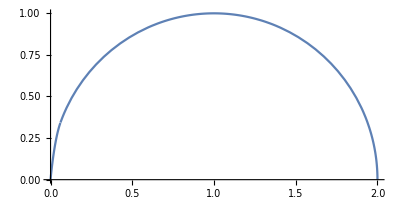

```mathematica
ParametricPlot[{1-Cos[x],Piecewise[{{InterpolatingPolynomial[{{0,0,0},{Pi/9,Sin[Pi/9],Cos[Pi/9]}},x],x<=Pi/9},{Sin[x],x>Pi/9}}]},{x,0,2*Pi}]
```

```mathematica
ParametricPlot[{1-Cos[x],Sin[x]*E^((-(x-Pi/2 )^2)/2)},{x,0,Pi}]
```

```mathematica
LaplaceTransform[10*x^3-15*x^4+6*x^5, x, p]
```

720/p^6-360/p^5+60/p^4

```mathematica
InverseLaplaceTransform[(720/p^6-360/p^5+60/p^4)*(1/(p^2+2*0.7*100*p+100^2)),p,t]
```

7.19888×10^-10-(3.59944×10^-10-4.36627×10^-9 ⅈ) ⅇ^((-70.-71.4143 ⅈ) t) ((-0.9865+0.163762 ⅈ)+(1.+0. ⅈ) ⅇ^((0.+142.829 ⅈ) t))+5.73236×10^-7 t-0.000043726 t^2+0.00108515 t^3-0.001542 t^4+0.0006 t^5

```mathematica
Simplify[%47]
```

7.19888×10^-10-(3.59944×10^-10+4.36627×10^-9 ⅈ) ⅇ^((-70.-71.4143 ⅈ) t)-(3.59944×10^-10-4.36627×10^-9 ⅈ) ⅇ^((-70.+71.4143 ⅈ) t)+5.73236×10^-7 t-0.000043726 t^2+0.00108515 t^3-0.001542 t^4+0.0006 t^5